# Blending Model Solution

Hello and welcome to the solution to our final project, part 1. As always, please try to solve the project yourself before watching this video.

## Introduction

In this lecture, we will make use of our project template. If you didn’t use the project template, you might want to open it up and follow along.

## Constants

First, let’s evaluate our constants:

```mathematica
xmin=0;xmax=50;
ymin=0;ymax=50;
```

We will make use of these throughout our code. The nice thing about declaring constants in a single place is that if you want to change them, there’s a single place where they can be changed.

## Creatures

Let’s evaluate our prototypical creatures, bc1 through bc4 which will be used in the tests:

```mathematica
bc1=BlendingCreature[0.1,{20,40}];
bc2=BlendingCreature[0.4,{30,40}];
bc3=BlendingCreature[0.7,{40,30}];
bc4=BlendingCreature[0.9,{40,20}];
```

## Accessors

On to our first function! The Traits function is nice and simple. It simply returns the one and only trait of our BlendingCreature. bc1’s trait is 0.1, bc2’s is 0.4 and so on. Therefore, the Traits of our creature is simply the first part of our BlendingCreature expression:

```mathematica
Traits[creature_BlendingCreature]:=creature[[1]]
```

Let’s run the appropriate test by opening the Tests section and evaluating our two Traits tests:

Great. Now let’s write our Location function. This is also simple. It returns the second part of our BlendingCreature:

```mathematica
Location[creature_BlendingCreature]:=creature[[2]]
```

Let’s test that out now:

### Tests

#### Verify the accessors

```mathematica
Traits[bc1]===0.1
```

```mathematica
Traits[bc2]===0.4
```

```mathematica
Location[bc3]==={40,30}
```

```mathematica
Location[bc4]==={40,20}
```

Awesome.

## Evolution

Now let’s write the functions that will evolve our creatures. The Procreate function produces a configurable number of offspring from two parent creatures:

```mathematica
Procreate[mother_BlendingCreature,father_BlendingCreature,OptionsPattern[{ChildCount->1}]]:=
(* So we start with Table *)
Table[
(* And we will be generating BlendingCreature expressions *)
BlendingCreature[
(* For the blending model, we will simply take the mean of the parent creatures' genes *)
Mean[{Traits[father],Traits[mother]}],
(* And for the location, we will generate a random location *)
{Random[Integer,{xmin,xmax}],Random[Integer,{ymin,ymax}]}
(* Close the BlendingCreature expression *)
],
(* And now we pass OptionValue[ChildCount] as the second argument to Table *)
OptionValue[ChildCount]
(* And finally, close the Table function call *)
]
```

Let’s test that out:

### Tests

#### Verify that Procreate of bc1 and bc2 produces offspring with trait value 0.25

```mathematica
MatchQ[Procreate[bc1,bc2],{BlendingCreature[0.25,{x_,y_}]}/;xmin≤x≤xmax&&ymin≤y≤ymax]
```

#### Verify that Procreate with ChildCount → 2 produces two offspring

```mathematica
MatchQ[Procreate[bc1,bc2,ChildCount->2],offspring:{BlendingCreature[0.25,_]..}/;Length[offspring]==2]
```

Awesome!

## Initialization

Next, the InitializeBlendingPopulation function will generate a population of blending creatures.

```mathematica
InitializeBlendingPopulation[size_Integer]:=
(* We'll use the Table function again *)
Table[
(* And it will generate BlendingCreature expressions *)
BlendingCreature[
(* The initial trait will be a random coin flip represented as either 0 or 1 *)
N@RandomChoice[{0,1}],
(* And the location will again be a random location *)
{Random[Integer,{xmin,xmax}],Random[Integer,{ymin,ymax}]}
(* Close the BlendingCreature expression *)
],
(* Now we pass how many creatures we're creating, which is size *)
size
(* And close the expression *)
]
```

Let’s test it out:

### Tests

#### Verify that InitializeBlendingPopulation returns 20 creatures

```mathematica
MatchQ[InitializeBlendingPopulation[20],creatures:{_BlendingCreature..}/;Length[creatures]==20]
```

Awesome!

## Simulation

Now we need a function that will evolve one generation into the next generation. The Evolve function must be stable, meaning that the number of creatures in the next generation must be equal to the number in the previous generation.

This function will be easier to write in pieces. Let’s start by generating a population:

```mathematica
population=InitializeBlendingPopulation[20]
```

Now, we need a random set of parents. We can do that by using RandomSample:

```mathematica
RandomSample[population]
```

And then Partition it into groups of 2 so that we pairs of parents:

```mathematica
Partition[RandomSample[population],2]
```

Now, we need to call Procreate on each pair, with a ChildCount of 2. We’ll create a pure function that gets passed the pairs of parents:

```mathematica
Procreate[#,ChildCount->2]&/@Partition[RandomSample[population],2]
```

The problem here is that the Procreate function is expecting the BlendingCreature expressions as a sequence, but it is currently being passed in as a list of two BlendingCreatures. Let’s modify our pure function to sequence the pairs of parents:

```mathematica
Procreate[Sequence@@#,ChildCount->2]&/@Partition[RandomSample[population],2]
```

Now we have a list of pairs of children. To turn this back into a population, we need to flatten it. We can use this final expression as our Evolve function:

```mathematica
Evolve[population:{__BlendingCreature}]:=Flatten[Procreate[Sequence@@#,ChildCount->2]&/@Partition[RandomSample[population],2]]
```

So, Evolve generates the next generation from the current generation. Now let’s write the BlendingSimulate function which will simulate all the generations in our simulation. Our starter notebook used two functions we haven’t seen in our classes before. The BlockRandom function is a function that localizes pseudorandom number generation and the SeedRandom function is a function that sets the current random number seed. Long story short, these functions allow our simulation to be repeatable for the same seed values.

In order to Evolve our population multiple times, we can use NestList:

```mathematica
NestList[Evolve,population,1]
```

The second argument is the number of iterations, which in terms of our simulation will be the number of generations!

When we put that into our function we will replace population with a call to InitializeBlendingPopulation:

```mathematica
BlendingSimulate[seed_Integer,numberOfGenerations_Integer,initialPopulationSize_Integer]:=
BlockRandom[
SeedRandom[seed];
NestList[Evolve,InitializeBlendingPopulation[initialPopulationSize],numberOfGenerations-1]
]
```

The extra credit question was: how would you modify BlendingSimulate so that it doesn’t recompute the simulation every time the function is called with the same arguments? In in a previous lecture, we showed how to cache Fibonacci evaluations. We will do the same here!

```mathematica
BlendingSimulate[seed_Integer,numberOfGenerations_Integer,initialPopulationSize_Integer]:=
BlockRandom[
SeedRandom[seed];
BlendingSimulate[seed,numberOfGenerations,initialPopulationSize]=NestList[Evolve,InitializeBlendingPopulation[initialPopulationSize],numberOfGenerations-1]
]
```

Now, if BlendingSimulate is called more than once for specific values of seed, numberOfGenerations and initialPopulationSize, the subsequent calls will return the previously cached values. Here’s the initial state:

```mathematica
?BlendingSimulate
```

Now we call BlendingSimulate with some concrete values:

```mathematica
BlendingSimulate[0,1,5]
```

And here’s the current state:

```mathematica
?BlendingSimulate
```

As you can see, we now have a cached value for BlendingSimulate[0, 1, 5]. Let’s run our corresponding tests:

### Tests

#### Verify that Evolving a population produces a new population of the same size

```mathematica
With[{initPop=InitializeBlendingPopulation[20]},
With[{nextGen=Evolve[initPop]},
And[
MatchQ[nextGen,creatures:{_BlendingCreature..}/;Length[creatures]==20],
nextGen=!=initPop
]
]]
```

#### Verify that the simulation is repeatable for the same arguments

```mathematica
BlendingSimulate[0,20,200]===BlendingSimulate[0,20,200]
```

#### Verify that the simulation produces different results for different seeds

```mathematica
BlendingSimulate[0,20,200]=!=BlendingSimulate[1,20,200]
```

Awesome!

## Rendering

Next, let’s evaluate the provided ColorBinarize function:

```mathematica
ColorBinarize[color_RGBColor]:=Round[Mean[List@@color]]/.{0->White,1->Black}
```

For HeredityColor, we’re simply going to pass the creature’s trait to the RGBColor function:

```mathematica
HeredityColor[creature_BlendingCreature]:=With[{
traits=Traits[creature]
},RGBColor[traits,traits,traits]]
```

CreatureName is going to be the rounded value of Traits:

```mathematica
CreatureName[creature_BlendingCreature]:=Round[Traits[creature],.1]
```

Now, let’s render a creature as a disk. We’ll prototype the creature first using bc4 as our prototypical creature. We will need it’s color and location, and we will be returning the graphics commands in a list:

```mathematica
Graphics[
With[{
color=HeredityColor[bc4],
location=Location[bc4]
},{
Disk[location,1]
}
],ImageSize->Tiny
]
```

Let’s make the border black, and the fill color equal to the heredity color:

```mathematica
Graphics[
With[{
color=HeredityColor[bc4],
location=Location[bc4]
},{
EdgeForm[Black],color,Disk[location,1]
}
],ImageSize->Tiny
]
```

Now, let’s add the creature’s name to the center. We will want the text to be dark if the fill is light and the text to be light if the fill is dark. This is where we will use our ColorBinarize function:

```mathematica
Graphics[
With[{
color=HeredityColor[bc4],
location=Location[bc4]
},{
EdgeForm[Black],color,Disk[location,1],
ColorBinarize[color],Text[CreatureName[bc4],location]
}
],ImageSize->Tiny
]
```

Awesome. Let’s copy the With function into our Render function, and replace bc4 with creature:

```mathematica
Render[creature_BlendingCreature]:=With[{
color=HeredityColor[creature],
location=Location[creature]
},{
EdgeForm[Black],color,Disk[location,1],
ColorBinarize[color],Text[CreatureName[creature],location]
}]
```

Our second render function will return the drawing commands to render a population of creatures. We can just map the creature Render function over the population:

```mathematica
Render[population:{___BlendingCreature}]:=Render/@population
```

Our TraitHistogram renders a histogram of the traits for a given population. So let’s prototype that:

```mathematica
Histogram[Traits/@population,{0,1.1,.1}]
```

Now, let’s make the bars match the color of the traits:

```mathematica
Histogram[Traits/@population,{0,1.1,.1},ChartStyle->Table[RGBColor[i,i,i],{i,0,1,0.1}]]
```

```mathematica
TraitHistogram[population:{___BlendingCreature}]:=Histogram[Traits/@population,{0,1.1,.1},ChartStyle->Table[RGBColor[i,i,i],{i,0,1,0.1}]]
```

Let’s run our tests!

### Tests

#### Verify that HeredityColor of bc1 is GrayLevel of 0.1

```mathematica
ColorConvert[HeredityColor[bc1],"RGB"]===RGBColor[0.1,0.1,0.1]
```

#### Verify that HeredityColor of bc2 is GrayLevel of 0.4

```mathematica
ColorConvert[HeredityColor[bc2],"RGB"]===RGBColor[0.4,0.4,0.4]
```

#### Verify that rendering a creature returns a list

```mathematica
MatchQ[Render[bc1],_List]
```

#### Verify that rendering a population returns a list

```mathematica
MatchQ[Render[InitializeBlendingPopulation[20]],_List]
```

#### Verify that we can render a column of graphics

This is not an automated test. Eyeball your render and make sure it looks like our render:

```mathematica
Column[{
TraitHistogram[BlendingSimulate[0,20,200][[2]]],
Graphics[Render[BlendingSimulate[0,20,200][[2]]],ImageSize->Large,PlotRange->{{xmin,xmax},{ymin,ymax}},ImagePadding->20]
}, Center]
```

Which should look something like:

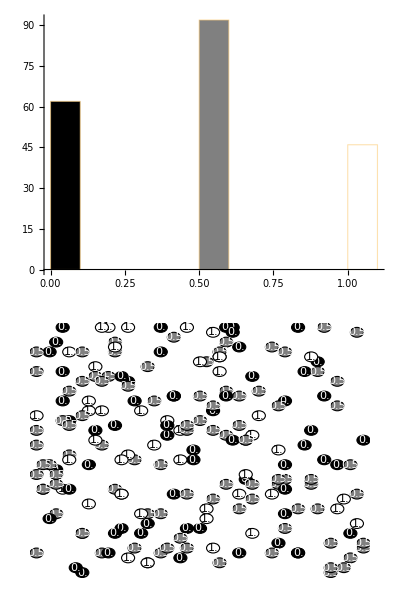

Awesome!

## Manipulate

We’re nearly there! Let’s render our population using Column:

```mathematica
Column[{
TraitHistogram[population],
Graphics[Render[population]]
}]
```

```mathematica
Column[{
TraitHistogram[population],
(* Let's make the Graphics section bigger: *)
Graphics[Render[population],ImageSize->Large]
}]
```

```mathematica
Column[{
TraitHistogram[population],
Graphics[Render[population],ImageSize->Large]
(* And now,let's center everything: *)
},Center]
```

```mathematica
(* 1. Let's wrap it up in the Manipulate *)
Manipulate[
Column[{
(* 4. And finally replace population with a call to BlendingSimulate, passing s and t *)
TraitHistogram[BlendingSimulate[s,20,200][[t]]],
Graphics[Render[BlendingSimulate[s,20,200][[t]]],ImageSize->Large]
},Center],
(* 2. We'll have an s variable for the seed *)
{{s,0,"Seed"},0,100,1},
(* 3. And a t variable for the generation *)
{{t,1,"Generation"},1,20,1}
]
```

There we have it! That’s our Blending model simulation. In the second part of this lecture, we will modify the simulator to include the Mendelian model. See you at the next lecture!